# Arithmetic parser

## Initialization

Finite state machine

```mathematica
Protect[ϵ]; (* ϵ will be used as a symbol to denote the empty string *)
Transition[parent_,child_,inputSymbol_]:=<|"Parent"->parent,"Node"->child,"InputSymbol"->inputSymbol|>;
EmptyTransition[parent_,child_]:=Transition[parent,child,ϵ];
FATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];
Concatenate[l_]:=Apply[Join,l];
```

```mathematica
NameTag[machine_Association,state_]:=Subscript[machine["Name"],ToString[state]];

Options[FAPlot]={"Legended"->True,"Labeled"->False};
FAPlot[machine_Association,OptionsPattern[]]:=Block[{graphData,startTag,acceptTags,legend,graph},
Switch[OptionValue["Labeled"],
True,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
,
False,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>p->n];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
];

legend = PointLegend[{LightBlue,Red,Green,Purple},{"State","Start state","Accept state","Start/Accept state"},LegendMarkers->Graphics[Disk[]]];

graph = Graph[
graphData,
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
];

If[OptionValue["Legended"],
Return[Legended[graph,legend]],
Return[graph]
]
];
```

```mathematica
(* DFA object constructor *)
DFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,(* Descriptive name to keep in track the regular operations applied to it *)
"Type"->"DFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept,
"StateExpressions"->stateExpr (* Each state may have an associated expression *)
|>;

(* Return every deterministic transition leading to state *)
DFATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];

(* Get the next state *)
Options[DFAIterate]={"Trace"->False};
DFAIterate[transitions_,state_,inputSymbol_,OptionsPattern[]]:=Block[{next},
next = Cases[
DFATransitions[transitions,state],
KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]
];

(* A DFA must have only one available transition *)
If[Length[next]==1,
If[OptionValue["Trace"],
Return[First[next]]
,
Return[First[next]["Node"]];
]
,
(* TODO: Crear mecanismo de alerta *)
Return[$Failed];
]
];

(* Returns the trace of the computation and the result of whether the machine accepts the inputString *)
DFACompute[machine_Association,inputString_]:=Block[{computation,result},
computation = FoldList[
DFAIterate[machine["Transitions"],#1["Node"],#2,"Trace"->True]&,
<|"Node"->machine["StartState"]|>,
inputString
];
result = MemberQ[machine["AcceptStates"],Last[computation]["Node"]];
Return[{computation,result}]
];
```

```mathematica
NFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,
"Type"->"NFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept ,
"StateExpressions"->stateExpr
|>;

ContainsQ[list_List,form_]:=MemberQ[list,form];
ContainsQ[form1_,form2_]:=form1===form2;

PureNondetStateQ[transitions_,state_]:=(DeleteDuplicates[FATransitions[transitions,state][[All,"InputSymbol"]]] === {ϵ});

(* Return the list of nodes accesible via empty transitions *)
NFANondetNodes[transitions_,state_Association]:=Cases[FATransitions[transitions,state["Node"]],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_Integer]:=Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_List]:=DeleteDuplicates[Flatten[Map[NFANondetNodes[transitions,#]&,state]]];
NFANondetNodesRecursive[transitions_,states_] := FixedPoint[DeleteDuplicates[Join[#,NFANondetNodes[transitions,#[[All,"Node"]]]]]&,states];

Options[NFAIterate]={"Trace"->False};
NFAIterate[transitions_,state_?AtomQ,inputSymbol_,OptionsPattern[]]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
(* Get all the transitions corresponding to a DFA *)
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

(* Run through the empty transitions of the DFA nodes *)
forkTransitions = NFANondetNodes[transitions,deterministicNodes]; (* Get past the current deterministic nodes *)
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions]; (* Append every valid nondet transition *)

(* The next nodes will be a union between the deterministic transitions and the nodes reachable from nondet transitions *)
next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,
If[OptionValue["Trace"],
Return[next],
Return[next[[All,"Node"]]]
]
,
Return[{}]
];
];
NFAIterate[transitions_,state_List,inputSymbol_,opt:OptionsPattern[]]:=DeleteDuplicates[Flatten[Map[NFAIterate[transitions,#,inputSymbol,opt]&,state]]];

NFACompute[machine_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[
machine["Transitions"],
{<|"Node"->machine["StartState"]|>}
];
computation = FoldList[
NFAIterate[machine["Transitions"],#1[[All,"Node"]],#2,"Trace"->True]&,
start,
inputString
];
result = Apply[Or,Map[MemberQ[machine["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];
```

```mathematica
TransitionApplyThreshold[transition_,threshold_]:=MapAt[#+threshold&,transition,{{Key["Parent"]},{Key["Node"]}}];
MachineApplyThreshold[machine_Association,threshold_]:=<|
"Name"->machine["Name"],
"Transitions"->Map[TransitionApplyThreshold[#,threshold]&,machine["Transitions"]],
"StartState"->machine["StartState"]+threshold,
"AcceptStates"->machine["AcceptStates"]+threshold,
"StateExpressions"->If[Length[machine["StateExpressions"]]≠ 0,MapAt[#+threshold&,machine["StateExpressions"],{All,1}],{}]
|>;
```

```mathematica
GetDirectSuccesors[machine_,state_]:=Select[
Nest[NFANondetNodes[machine["Transitions"],#]&,{state},2],
(!ContainsQ[machine["AcceptStates"],#["Parent"]] &&PureNondetStateQ[machine["Transitions"],#["Parent"]] && Length[FAParents[machine["Transitions"],#["Parent"]]]==1)
&
];

ReplaceKey[assoc_,key_,replaceTo_]:=MapAt[replaceTo&,assoc,Key[key]];

DeleteIntermediateTransition[transitions_,startState_,endState_]:=Block[{deleteState,replacement,newTransitions,cleanedUp},
deleteState = endState["Parent"];
replacement = ReplaceKey[endState,"Parent",startState["Node"]];
cleanedUp = DeleteCases[transitions,KeyValuePattern["Parent"->deleteState]];
cleanedUp = DeleteCases[cleanedUp,KeyValuePattern["Node"->deleteState]];

newTransitions = Append[cleanedUp,replacement];
Return[newTransitions];
];

SimplifyStateIteration[nfa_,state_]:=Block[{newMachine,newTransitions},
newMachine = nfa;
newTransitions = Fold[
DeleteIntermediateTransition[#1,<|"Node"->state|>,#2]&,
nfa["Transitions"],
GetDirectSuccesors[nfa,state]
];
newMachine["Transitions"] = newTransitions;
Return[newMachine];
];
SimplifyState[nfa_,state_]:=FixedPoint[SimplifyStateIteration[#,state]&,nfa];

SimplifyMachine[nfa_]:=Block[{simplified,oldStates,newStates,stateRelabelRule = {}},
simplified = Fold[SimplifyState,nfa,GetStates[nfa["Transitions"]]];

oldStates = GetStates[simplified["Transitions"]];
newStates = Range[0,Length[oldStates]-1];
stateRelabelRule = Thread[oldStates->newStates];

simplified["Transitions"] = DeleteDuplicates[MapAt[Replace[#,stateRelabelRule]&,simplified["Transitions"],{{All,Key["Parent"]},{All,Key["Node"]}}]];
simplified["StartState"] = Replace[simplified["StartState"],stateRelabelRule];
simplified["AcceptStates"] = ReplaceAll[simplified["AcceptStates"],stateRelabelRule];
If[Length[simplified["StateExpressions"]]≠ 0,
simplified["StateExpressions"] = MapAt[Replace[#,stateRelabelRule]&,simplified["StateExpressions"],{All,1}];
];
Return[simplified];
];
```

```mathematica
NFAUnion[machine1_Association,machine2_Association]:=Block[{minIndex,newIndexThreshold,newM1,newM2,newAccept,newTransitions,newMachine,newStateExpressions},
minIndex = Min[machine1["Transitions"][[All,"Parent"]]];
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM1 = MachineApplyThreshold[machine1,1];
newM2 = MachineApplyThreshold[machine2,newIndexThreshold+1];
newAccept = Sort[Join[newM1["AcceptStates"],newM2["AcceptStates"]]];
newTransitions = {EmptyTransition[minIndex,newM1["StartState"]], EmptyTransition[minIndex,newM2["StartState"]]};
newStateExpressions = SortBy[Join[newM1["StateExpressions"],newM2["StateExpressions"]],First];

newMachine = <|
"Name"->StringJoin[machine1["Name"],"∪",machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[newM1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAUnion[machines__/;Length[List[machines]]>2]:=Fold[NFAUnion,First[List[machines]],Rest[List[machines]]];
```

```mathematica
NFAConcatention[machine1_Association,machine2_Association]:=Block[{newIndexThreshold,newM2,newTransitions,newMachine,newStateExpressions},
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM2 = MachineApplyThreshold[machine2,newIndexThreshold];

newTransitions = Map[EmptyTransition[#,newM2["StartState"]]&,machine1["AcceptStates"]];

newStateExpressions = Join[machine1["StateExpressions"],newM2["StateExpressions"]];
newStateExpressions = If[Length[newStateExpressions]≠ 0,SortBy[Join[machine1["StateExpressions"],newM2["StateExpressions"]],First],{}];

newMachine = <|
"Name"->StringJoin[machine1["Name"],machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[machine1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->machine1["StartState"],
"AcceptStates"->newM2["AcceptStates"],
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAConcatention[machines__/;Length[List[machines]]>2]:=Fold[NFAConcatention,First[List[machines]],Rest[List[machines]]];
```

```mathematica
NFAStar[machine_Association]:=Block[{minIndex,newM,newTransitions,newAccept,newMachine},
minIndex = Min[machine["Transitions"][[All,"Parent"]]];
newM = MachineApplyThreshold[machine,1];
newTransitions = Join[{EmptyTransition[minIndex,newM["StartState"]]},Map[EmptyTransition[#,newM["StartState"]]&,newM["AcceptStates"]]];
newAccept = Append[newM["AcceptStates"],minIndex];

newMachine = <|
"Name"->StringJoin["(",machine["Name"],")^*"],
"Type"->"NFA",
"Transitions"->Join[newM["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newM["StateExpressions"]
|>;
Return[newMachine];
];
```

```mathematica
(* Check if there is at least one of the accepted states in searchState *)
ContainsStateQ[stateList_,searchState_?AtomQ]:=MemberQ[stateList,searchState];
ContainsStateQ[stateList_,searchState_List]:=Apply[Or,Map[MemberQ[stateList,#]&,searchState]];

(* Get parents of the current state *)
FAParents[transitions_,state_]:=DeleteDuplicates[Cases[transitions,KeyValuePattern[{"Node"->state}]][[All,"Parent"]]];

(* Check if the state is inaccesible *)
JunkStateQ[transitions_,start_,state_]:=Block[{stateParents,nonSelfTransitions},
If[ContainsStateQ[start,state],Return[False]];
stateParents = FAParents[transitions,state];
nonSelfTransitions = Complement[stateParents,{state}];
If[Length[nonSelfTransitions]==0,
Return[True],
Return[False]
]
];

SafeSort[l_List]:=Sort[l];
SafeSort[l_?AtomQ]:=l;

(* Infer the alphabet from the transition list *)
GetAlphabet[transitions_]:=DeleteCases[DeleteDuplicates[Flatten[transitions[[All,"InputSymbol"]]]],ϵ];

(* Infer the states from the transition list *)
GetStates[transitions_]:=Sort[DeleteDuplicates[Flatten[Cases[transitions,KeyValuePattern[{"Parent"->p_,"Node"->n_}]:>{p,n}]]]];

(* Get the states reachable from the current states list *)
Explore[transitions_,states_]:=Map[
Transition[
SafeSort[states],
SafeSort[DeleteDuplicates[NFAIterate[transitions,states,#,"Trace"->False]]],
{#}]&,
GetAlphabet[transitions]
];

(* Explore one step down each branch of the computation and append it to the explored branches list *)
StepDown[transitions_,branches_]:=DeleteDuplicates[
Flatten[
Join[
branches,
Map[
Explore[
transitions,
#["Node"]
]&,
branches
]
],
1]
];

NewStateNode[node_,newStateRules_]:=
<|
"Parent"->Replace[node["Parent"],newStateRules],
"Node"->Replace[node["Node"],newStateRules],
"InputSymbol"->node["InputSymbol"]
|>;

NFAToDFA[machine_Association]:=Block[{protoDFA,start,protoDFAStates,newStateRules,newStates,containsAccept,newMachine,newAccept,newStart,newTransitions,newTransitionsCleanedUp,protoDFAExpressionNodes,newStateExpressionsNodes},
If[machine["Type"] =!= "NFA",Return[$Failed]];

(* Explore all paths until there is no unexplored transition *)
start = 
FixedPoint[
DeleteDuplicates[
Join[
#,
NFANondetNodes[machine["Transitions"],#[[All,"Node"]]]]
]&,
{<|"Node"->machine["StartState"]|>}
];

(* Make a DFA by exploring all possible paths in the NFA *)
protoDFA = FixedPoint[StepDown[machine["Transitions"],#]&,{<|"Node"->start[[All,"Node"]]|>}];
protoDFAStates = DeleteDuplicates[Join[Drop[protoDFA,1][[All,"Parent"]],Drop[protoDFA,1][[All,"Node"]]]];

(* Match old NFA parameters to the new DFA *)
newStateRules = Thread[protoDFAStates->Range[Length[protoDFAStates]]];
newStates =newStateRules[[All,2]];
containsAccept = Position[protoDFAStates,s_/;ContainsStateQ[s,machine["AcceptStates"]]];
newAccept = Extract[newStates,containsAccept];
newStart = Replace[First[protoDFAStates],newStateRules];
newTransitions = Map[NewStateNode[#,newStateRules]&,Drop[protoDFA,1]];
newTransitionsCleanedUp = DeleteDuplicates[DeleteCases[newTransitions,t_/; JunkStateQ[newTransitions,newStart,t["Node"]]]];

protoDFAExpressionNodes = Concatenate[
Map[
Thread[Cases[protoDFAStates,s_/;ContainsStateQ[s,First[#]]]->Last[#]]&,
machine["StateExpressions"]
]
];
If[Length[protoDFAExpressionNodes]≠0,
newStateExpressionsNodes = MapAt[Replace[#,newStateRules]&,protoDFAExpressionNodes,{All,1}]
,
newStateExpressionsNodes = {}
];

newMachine = <|
"Name"->machine["Name"],
"Type"->"DFA",
"Transitions"->newTransitionsCleanedUp,
"StartState"->newStart,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressionsNodes
|>;
Return[newMachine];
];
```

Regular expressions

```mathematica
RegexUnion[args__]:=NFAUnion[args];
RegexConcatenation[args__]:=NFAConcatention[args];
RegexStar[machine_Association]:=NFAStar[machine];
RegexStar[c_String]:=NFAStar[Regex[c]];
RegexDagger[machine_Association]:=NFAConcatention[machine,NFAStar[machine]];
RegexDagger[c_String]:=NFAConcatention[Regex[c],NFAStar[Regex[c]]];
```

```mathematica
Regex[c_String/;StringLength[c]==1]:=NFA[c,{Transition[0,1,{c}]},0,{1}];
Regex[c_String/;StringLength[c]==1,stateExpr_]:=NFA[c,{Transition[0,1,{c}]},0,{1},{1->stateExpr}];
Regex[s_String/;StringLength[s]>1,tokenRecognize_:""]:=Block[{m},
m =Apply[NFAConcatention,Map[Regex,Characters[s]]];
If[tokenRecognize≠ "",
m["StateExpressions"] =Thread[m["AcceptStates"]->tokenRecognize];
];

Return[m];
];
Regex[r_Association,tokenRecognize_]:=Block[{m = r},
m["StateExpressions"] = Thread[m["AcceptStates"]->tokenRecognize];
Return[m];
];
```

```mathematica
RegexAlphabet[alphabet_]:=Block[{input,name,transitions,acceptStates,newMachine},
input = Characters[alphabet];
newMachine = <|
"Name"->StringJoin[Riffle[input,"∪"]],
"Type"->"NFA",
"Transitions"->Map[Transition[0,#,{input[[#]]}]&,Range[Length[input]]],
"StartState"->0,
"AcceptStates"->Range[Length[input]],
"StateExpressions"->{}
|>;
Return[newMachine];
];

RegexAlphabetLowercase[]:=RegexAlphabet[StringJoin@Alphabet[]];
RegexAlphabetUppercase[]:=RegexAlphabet[StringJoin@ToUpperCase[Alphabet[]]];
RegexAlphabet[]:=RegexAlphabet[StringJoin@Join[Alphabet[],ToUpperCase[Alphabet[]]]];
RegexDigits[]:=RegexAlphabet[StringJoin@Map[ToString,Range[0,9]]];

asciiChars = {"\t","\n","\f","\r"," ","!","#","$","%","&","'","(",")","*","+",",","-",".","/","0","1","2","3","4","5","6","7","8","9",":",";","<","=",">","?","@","A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z","[","\\","]","^","_","`","a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z","{","|","}","~",".7f"};

RegexASCIIChars[]:=RegexAlphabet[StringJoin@asciiChars];
```

```mathematica
RegexCompute[machine_,input_]:=Block[{trace,result,recognizedTokens},
If[machine["Type"]== "NFA",
{trace,result} = NFACompute[machine,Characters[input]];
recognizedTokens = 
Cases[
Last[trace][[All,"Node"]],
(node_ /; ContainsQ[machine["StateExpressions"][[All,1]],node]):> Replace[node,machine["StateExpressions"]]
];

,
{trace,result} =DFACompute[machine,Characters[input]];
recognizedTokens = 
Cases[
{Last[trace]["Node"]},
(node_ /; ContainsQ[machine["StateExpressions"][[All,1]],node]):> Replace[node,machine["StateExpressions"]]
];
];

Return[{trace,result,recognizedTokens}];
];
```

Lexer

```mathematica
Token[symbol_String,name_String]:=<|"Class"->"Token","Symbol"->symbol,"Name"->name|>;
```

```mathematica
TokenKeyword[symbol_String,name_String]:=<|"Class"->"TokenKeyword","Symbol"->symbol,"Name"->name|>;
```

```mathematica
GetToken[input_,symbolTokens_,keywordTokens_]:=Block[{symbolAccept,symbolResult,keywordAccept,keywordResult},
{symbolAccept,symbolResult} = Rest[RegexCompute[symbolTokens,input]];
{keywordAccept,keywordResult} = Quiet[Rest[RegexCompute[keywordTokens,input]]];
If[keywordAccept,Return[First[keywordResult]]];
If[symbolAccept,Return[First[symbolResult]]];
Return["Nothing"];
];

SafeStringTake[string_,n_]:=StringTake[string,Min[n,StringLength[string]]];
SafeStringTake[string_,{m_,n_}]:=StringTake[string,{m,Min[n,StringLength[string]]}];

GetNextToken[program_,symbolTokens_,keywordTokens_]:=Block[{tokenizerResult,nextToken},
tokenizerResult = NestWhileList[
{
First[#]+1,
GetToken[SafeStringTake[program,First[#]+1],symbolTokens,keywordTokens]
}&,
{
0,
None
},
((Last[#]=!= "Nothing")&&(First[#]≤StringLength[program]))&
];

nextToken = If[Length[tokenizerResult]>2,tokenizerResult[[-2]],Last[tokenizerResult]];
Return[nextToken];
];

SafeMod[m_,0]:=m;
SafeMod[m_,n_]:=Mod[m,n];
LinePosition[pos_,lineBreaks_]:=SafeMod[pos,Last[Select[Prepend[lineBreaks+1, 0],#≤pos&]]];
ColumnPosition[pos_,lineBreaks_]:=Position[Ordering[Prepend[lineBreaks, pos]],1][[1,1]]-1;

Options[Tokenize]={"IncludeLineBreaks"->False};
Tokenize[program_,symbolTokens_,keywordTokens_,OptionsPattern[]]:=Block[
{
length,type,
cursor = 0,
tokenList = {},
inComment = False,
omitTokens = {"Whitespace","LineComment"},
breaks,positionMappedTokens,formattedTokens
},

While[cursor<StringLength[program],
{length,type} = GetNextToken[StringDrop[program,cursor],symbolTokens,keywordTokens];
If[inComment,
If[type == "LineBreak",
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
inComment = False;
];
,

If[!MemberQ[omitTokens,type],
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
];
];
cursor+=length;
If[type == "LineComment",inComment = True];
];

breaks = Cases[tokenList,KeyValuePattern[{"Position"->p_,"Type"->"LineBreak"}]:>p];
positionMappedTokens = Map[
If[#["Type"] =!=#["Value"],
<|
"Type"->#["Type"],
"Value"->#["Value"]
|>,
<|
"Type"->#["Type"]
|>
]
&,
tokenList
];
If[OptionValue["IncludeLineBreaks"],
Return[positionMappedTokens];
,
formattedTokens = DeleteCases[positionMappedTokens,KeyValuePattern["Type"->"LineBreak"]];
Return[formattedTokens];
];
];
```

Parser

```mathematica
MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];
```

```mathematica
Protect[EmptyString,Term,NonTerm];

GetArgument[_[arg_]]:=arg;
Substitute[l1_,l2_]:=Join[l1,Drop[l2,Length[l1]]];

TermMatchQ[input_,{}]:=True;
TermMatchQ[input_,terms_]:=(Take[input,Length[terms]][[All,"Type"]] == Map[GetArgument,terms]);
GenerateTransition[rule_,stateId_,lastId_]:=MapIndexed[{rule["From"],stateId}->{#1,lastId+First[#2]}&,rule["To"]];

MatchTerminalsWithRule[stateId_,lastId_,input_,rule_]:=Block[{terms,transition,rest,cuttedInput,currentState,lastIndex,matchTransitions},

currentState = rule["From"];
If[rule["To"]===EmptyString,Return[{{{currentState,stateId}->{EmptyString,lastId+1}},{},input,lastId+1}]];

transition = GenerateTransition[rule,stateId,lastId];
lastIndex = Last@Last@Last@transition;
terms = TakeWhile[rule["To"],Head[#]=!=NonTerm&];
rest = Drop[transition[[All,2]],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[TermMatchQ[input,terms],
matchTransitions =MapIndexed[
If[KeyExistsQ[#1,"Value"],
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2],#1["Value"]},
{rule["From"],stateId}->{Term[#1["Type"]],lastId+First[#2]}
]&,
Take[input,Length[terms]]
];
transition = Substitute[matchTransitions,transition];

cuttedInput = Drop[input,Length[terms]];
Return[{transition,rest,cuttedInput,lastIndex}];
,
Return[$Failed];
];
];

MatchTerminals[{state_,stateId_},lastId_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[MatchTerminalsWithRule[stateId,lastId,input,#]&,possibleTransitions,#=!=$Failed&]];
Return[matched];
];
```

```mathematica
Parse[input_,grammar_]:=Block[{stack,transitions,next,inputBuffer,lastId,parseTree,parseSymbol,toStack},
stack = {};
parseTree = {};
lastId = 1;
inputBuffer = input;
parseSymbol = {First[grammar]["From"],1};

While[{inputBuffer,parseSymbol} =!= {{},None},
If[Head[First[parseSymbol]] ===NonTerm,
{transitions,next,inputBuffer,lastId} = MatchTerminals[parseSymbol,lastId,inputBuffer,grammar];
AppendTo[parseTree,transitions];
,
If[GetArgument[First[parseSymbol]] == First[inputBuffer]["Type"],
inputBuffer =Drop[inputBuffer,1];
next = {};
];
];

If[Length[next]>0,
(* Push *)
{parseSymbol,toStack}={First[next],Rest[next]};
stack = Join[stack,toStack];
,
(* Pop *)
If[Length[stack] > 0,
{parseSymbol,stack}={Last[stack],Drop[stack,-1]};
,
parseSymbol = None;
];
];
];

Return[Flatten[parseTree,1]];
];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction},
parseTree = Parse[input,grammar];
startProduction = First[First[parseTree]];

TreePlot[parseTree,Automatic,startProduction,VertexLabeling->True]
];
```

## Implementation

```mathematica
tokenSymbols = Map[
Token[#[[1]],#[[2]]]&,
{
{" ","Whitespace"},
{"*", "*"},
{"+", "+"},
{"(", "("},
{")", ")"}
}
];
```

```mathematica
tokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenSymbols]]];
tokenSymbolsDFA = NFAToDFA[tokenSymbolsNFA];
```

```mathematica
idLiteral = Regex[NFAToDFA[RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]]],"id"];
```

```mathematica
tokens = Tokenize["56*(23+1)",tokenSymbolsDFA,idLiteral]
```

{<|Type→id,Value→56|>,<|Type→*|>,<|Type→(|>,<|Type→id,Value→23|>,<|Type→+|>,<|Type→id,Value→1|>,<|Type→)|>}

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>,

<|"From"->NonTerm["T"],"To"->{NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->{Term["*"],NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->EmptyString|>,

<|"From"->NonTerm["F"],"To"->{Term["id"]}|>,
<|"From"->NonTerm["F"],"To"->{Term["("],NonTerm["E"],Term[")"]}|>
};
```

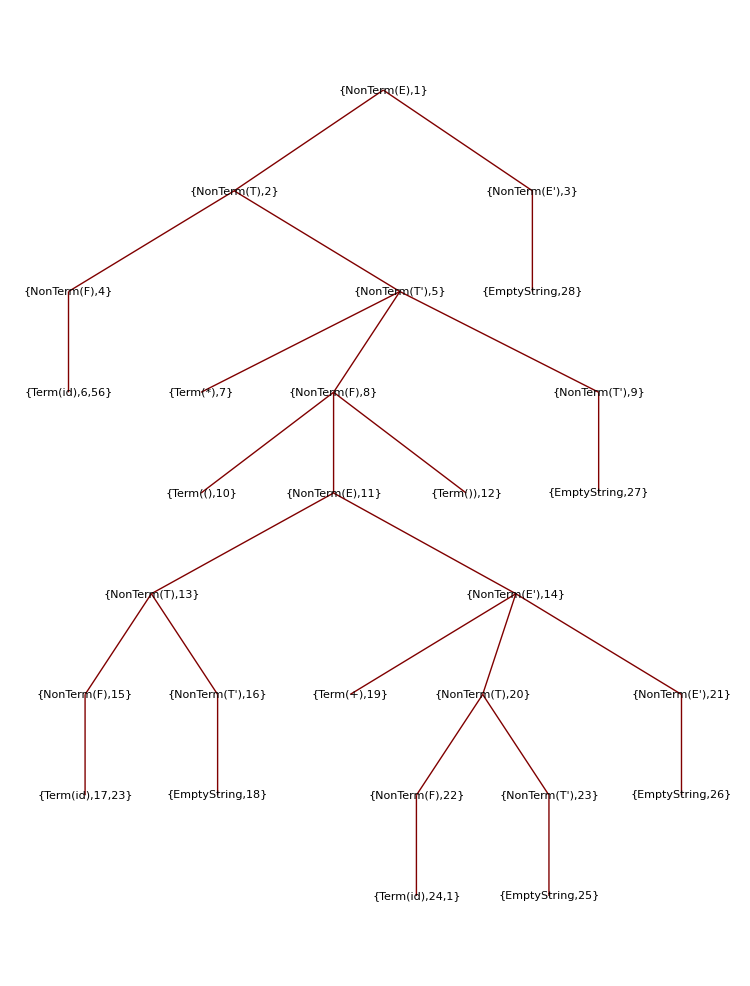

```mathematica
ParseTree[tokens,grammar]
```

```mathematica
ast = Parse[tokens,grammar] ;
```

```mathematica
BreadthFirstScan[Graph[ast],{NonTerm["E"],1},{"PrevisitVertex"->(Print[#]&)}];
```

{NonTerm[E],1}

{NonTerm[T],2}

{NonTerm[E'],3}

{NonTerm[F],4}

{NonTerm[T'],5}

{EmptyString,28}

{Term[id],6,56}

{Term[*],7}

{NonTerm[F],8}

{NonTerm[T'],9}

{Term[(],10}

{NonTerm[E],11}

{Term[)],12}

{EmptyString,27}

{NonTerm[T],13}

{NonTerm[E'],14}

{NonTerm[F],15}

{NonTerm[T'],16}

{Term[+],19}

{NonTerm[T],20}

{NonTerm[E'],21}

{Term[id],17,23}

{EmptyString,18}

{NonTerm[F],22}

{NonTerm[T'],23}

{EmptyString,26}

{Term[id],24,1}

{EmptyString,25}